# Load first-order Lorenz gauge metric perturbation data from the h1Lorenz code

This notebook uses SimulationTools which you can download from: https://simulationtools.org/

```mathematica
<<SimulationTools`
```

## Define function Loadh1Data[r0,l,m] to load the h1 data

```mathematica
fieldOrder[l_,m_]/;EvenQ[l+m]:=If[m==0,{1,3,5,6,7,2,4},{1,3,5,6,7,2,4}]
fieldOrder[0,0]:={1,3,6,2}
fieldOrder[1,0]:={9,8}
fieldOrder[1,1]:={1,3,5,6,2,4}
fieldOrder[l_,m_]/;OddQ[l+m]:=If[m==0,{9,10,8},{9,10,8}]
```

```mathematica
Loadh1Data[r0_,l_,m1_]:=Module[{gridJ, r0PosJ, tmp,m=m1,fields},
SetDirectory[NotebookDirectory[]<>"../data/fields_r"<>ToString[r0]];

gridJ=ImportHDF5["h1-l"<>ToString[l]<>"m"<>ToString[m1]<>".h5",{"Datasets","/grid"}];
r0PosJ=Position[gridJ,N[r0]][[1,1]];
gridJ=Insert[gridJ,N[r0],r0PosJ+1];

fields=fieldOrder[l,m1];

tmp=Map[Flatten,Transpose@{gridJ,Join[ImportHDF5["h1-l"<>ToString[l]<>"m"<>ToString[m1]<>".h5",{"Datasets","inhom_left"}],ImportHDF5["h1-l"<>ToString[l]<>"m"<>ToString[m1]<>".h5",{"Datasets","inhom_right"}]]}];
Do[h1[r0][fields[[j]],l,m]=ToDataTable[Table[{tmp[[k,1]],tmp[[k,2+4(j-1)]]+I tmp[[k,3+4(j-1)]]},{k,1,Length[gridJ]}]],{j,1,Length[fields]}];
Do[drh1[r0][fields[[j]],l,m]=ToDataTable[Table[{tmp[[k,1]],tmp[[k,4+4(j-1)]]+I tmp[[k,5+4(j-1)]]},{k,1,Length[gridJ]}]],{j,1,Length[fields]}];
]
```

```mathematica
Loadh1Data[10,2,2]
```

## Example of loading the data

```mathematica
Loadh1Data[6,2,2]
Loadh1Data[6,2,1]
```

After you use Loadh1Data you can find the data in h1[r0][i,l,m] and drh1[r0][i,l,m]

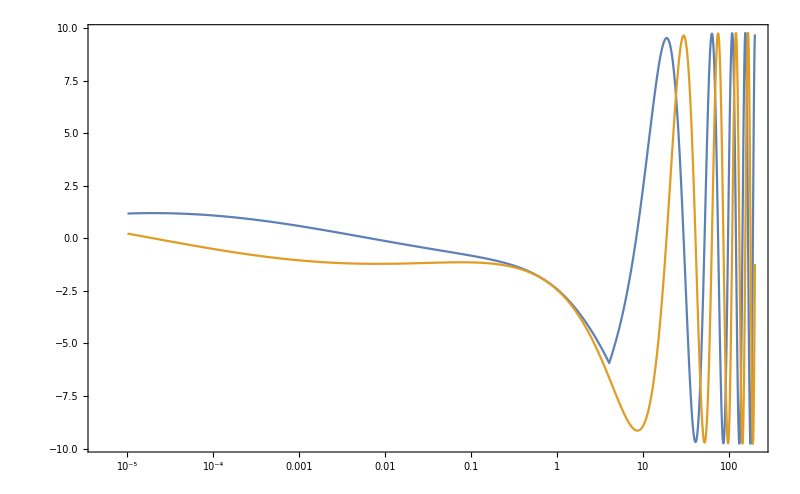

```mathematica
ListLogLinearPlot[Shifted[Slab[h1[6][7,2,2],2;;200],-2]//ReIm,Joined->True,ImageSize->800,PlotTheme->"Detailed",PlotRange->All]
```

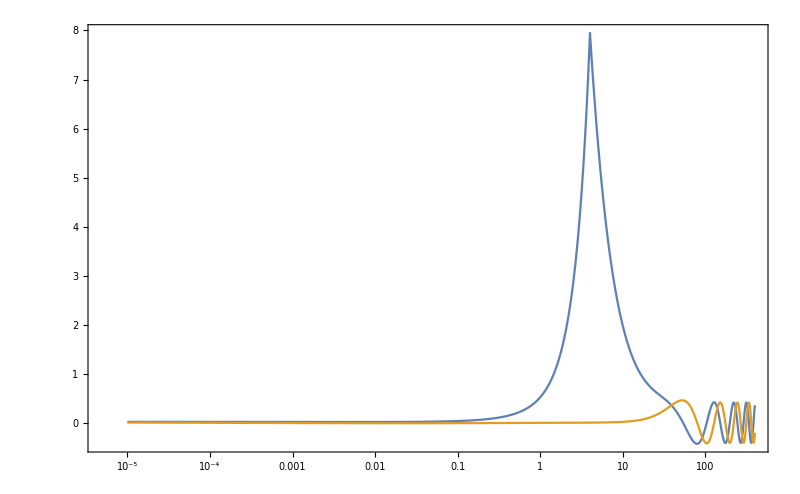

```mathematica
ListLogLinearPlot[Shifted[Slab[h1[6][8,2,1],2;;400],-2]//ReIm,Joined->True,ImageSize->800,PlotTheme->"Detailed",PlotRange->All]
```

To get the radial values of the data use, e.g.,

```mathematica
ToListOfCoordinates[h1[6][1,2,2]];
```

To get a regular list of the data use:

```mathematica
ToList[h1[6][1,2,2]]
```

{{2.00001,-0.00584021+0.00946877 ⅈ},{2.00002,-0.00396092+0.0103957 ⅈ},{2.00003,-0.00279202+0.0107683 ⅈ},{2.00004,-0.00194129+0.0109534 ⅈ},3340,{9970.,0.0798373-1.55275 ⅈ},{9980.,1.53535-0.245137 ⅈ},{9990.,0.559372+1.45069 ⅈ},{10000.,-1.30247+0.8491 ⅈ}}
 |  |  |  |